## 6.859 A4: Does Charlie WFH?

## Georgios Varnavides, Max L’Etoille

## 2010 Census Tracts

### Shapefiles

```mathematica
SetDirectory[FileNameDrop[NotebookDirectory[],-2]]
```

/home/george/Documents/git-repos/a4-does-charlie-wfh

```mathematica
censusTracts["Middlesex"]=Association[Import["data/tl_2010_25017_tract10.zip","Data"][[1]]];
censusTracts["Norfolk"]=Association[Import["data/tl_2010_25021_tract10.zip","Data"][[1]]];
censusTracts["Suffolk"]=Association[Import["data/tl_2010_25025_tract10.zip","Data"][[1]]];
```

```mathematica
GeoGraphics[{
EdgeForm[Black],FaceForm[None],
censusTracts["Middlesex"]["Geometry"],
Delete[censusTracts["Norfolk"]["Geometry"],85],
Delete[censusTracts["Suffolk"]["Geometry"],56]
}]
```

```mathematica
censusTractsPolygonsAsc=KeyDrop[KeyMap[ToExpression,Join@@Table[AssociationThread[Association[censusTracts[county]["LabeledData"]]["TRACTCE10"]->censusTracts[county]["Geometry"]],{county,{"Middlesex","Norfolk","Suffolk"}}]],{990101,423100}];
```

### MBTA Lines

```mathematica
(*see mbta-shapefiles.nb*)
```

```mathematica
Keys[shapeFilesAssociations=With[{fileName="data/mbta_rapid_transit.zip"},
Association/@AssociationThread[Import[fileName,"LayerNames"]->Import[fileName,"Data"]]]]
geometryAssociations=Map[#["Geometry"]/. {Line[x_]:>(Line[GeoGridPosition[#,"SPCS83MA01"]&/@x]),Point[x_]:>Point[GeoGridPosition[x,"SPCS83MA01"]]}&,shapeFilesAssociations];
```

{MBTA_ARC,MBTA_NODE}

```mathematica
groupedRoutesByLine=KeySort[With[{lineMetaData=Association[shapeFilesAssociations["MBTA_ARC","LabeledData"]]["LINE"]},
GroupBy[Thread[{Range[Length[lineMetaData]],lineMetaData}],Last][[All,All,1]]]];
```

```mathematica
splitSharedStations[key_,value_]:=Block[{stations},
stations=StringSplit[key,"/"];
<|stations[[1]]->value,stations[[2]]->value|>]

groupedStationsByLineTmp=KeySort[With[{lineMetaData=Association[shapeFilesAssociations["MBTA_NODE","LabeledData"]]["LINE"]},
GroupBy[Thread[{Range[Length[lineMetaData]],lineMetaData}],Last][[All,All,1]]]];
sharedStationsAsc=KeySelect[groupedStationsByLineTmp,StringContainsQ["/"]];
groupedStationsByLine=KeySort[KeyDrop[Flatten/@Merge[{groupedStationsByLineTmp,Flatten/@Merge[KeyValueMap[splitSharedStations,sharedStationsAsc],Identity]},Identity],Keys[sharedStationsAsc]]];
```

```mathematica
cleanedUpRoutesByLine=KeySort@KeyDrop[groupedRoutesByLine,"SILVER"];
cleanedUpCols={Interpreter["Color"]["#244995"],Interpreter["Color"]["#118342"],Interpreter["Color"]["#ef7d15"],Interpreter["Color"]["#e22224"]}
```

{RGBColor[Rational[12, 85], Rational[73, 255], Rational[149, 255]],RGBColor[Rational[1, 15], Rational[131, 255], Rational[22, 85]],RGBColor[Rational[239, 255], Rational[25, 51], Rational[7, 85]],RGBColor[Rational[226, 255], Rational[2, 15], Rational[12, 85]]}

Second, we ‘bin’ stations w/ multiple entrances to one GeoPosition

Turns out there’s only one such pair once we remove the silver line nodes

St. Paul St on GL-C with two locations ~0.5 mile apart

We pick the one on Comm Ave

```mathematica
positionDuplicates[list_]:=GatherBy[Range@Length[list],list[[#]]&]
```

```mathematica
Select[DeleteCases[#,Alternatives@@groupedStationsByLine["SILVER"]]&/@positionDuplicates[Lookup[Association[shapeFilesAssociations["MBTA_NODE","LabeledData"]],"STATION"]],Length[#]>1&]
Lookup[Association[shapeFilesAssociations["MBTA_NODE","LabeledData"]],"STATION"][[First[%]]]
GeoDistance@@GeoPosition/@geometryAssociations["MBTA_NODE"][[First[%%],1]]
```

{{82,105}}

{Saint Paul Street,Saint Paul Street}

0.550605 mi

```mathematica
cleanedUpStations=Delete[Transpose[Append[Lookup[Association[shapeFilesAssociations["MBTA_NODE","LabeledData"]],{"STATION","LINE"}],GeoPosition/@geometryAssociations["MBTA_NODE"][[All,1]]]],List/@Append[groupedStationsByLine["SILVER"],105]];

splitSharedStationsClean[row_]:=If[StringContainsQ["/"][row[[2]]],
Table[{row[[1]],station,row[[3]]},{station,StringSplit[row[[2]],"/"]}],{row}]

cleanedUpStations=SortBy[Flatten[splitSharedStationsClean/@cleanedUpStations,1],#[[2]]&];
cleanedUpStationsByLine=KeySort[GroupBy[cleanedUpStations,#[[2]]&]];
```

### Neighborhood Covariates

```mathematica
data=Import["data/tract_covariates.csv","Data"];
data=Select[data,#[[1]]==25&&(#[[2]]==17||#[[2]]==21||#[[2]]==25)&];
```

```mathematica
Import["data/tract_covariates.csv",{"Data",1}]
```

{state,county,tract,cz,czname,hhinc_mean2000,mean_commutetime2000,frac_coll_plus2000,frac_coll_plus2010,foreign_share2010,med_hhinc1990,med_hhinc2016,popdensity2000,poor_share2010,poor_share2000,poor_share1990,share_white2010,share_black2010,share_hisp2010,share_asian2010,share_black2000,share_white2000,share_hisp2000,share_asian2000,gsmn_math_g3_2013,rent_twobed2015,singleparent_share2010,singleparent_share1990,singleparent_share2000,traveltime15_2010,emp2000,mail_return_rate2010,ln_wage_growth_hs_grad,jobs_total_5mi_2015,jobs_highpay_5mi_2015,popdensity2010,ann_avg_job_growth_2004_2013,job_density_2013}

```mathematica
censusMap=Block[{
cf=ResourceFunction["ColorBrewerData"]["BrBG","ColorFunction"],
mbtaLines,
medianHouseholdIncome
},

medianHouseholdIncome=DeleteCases[Thread[Lookup[censusTractsPolygonsAsc,data[[All,3]],FilledCurve[]]->data[[All,12]]]/.""->Missing[],_FilledCurve->_];

(*likely requires evaluating mbta-shapefiles.nb*)
mbtaLines=GeoGraphics[{
MapThread[{Thick,#1,geometryAssociations["MBTA_ARC"][[cleanedUpRoutesByLine[#2]]]}&,{cleanedUpCols,cleanedUpRoutesByLine//Keys}],MapThread[{PointSize[Large],#1,Point[cleanedUpStationsByLine[#2][[All,3]]]}&,{cleanedUpCols,cleanedUpStationsByLine//Keys}]},GeoBackground->None];

GeoRegionValuePlot[medianHouseholdIncome,MissingStyle->GrayLevel[0.15],GeoBackground->None,ColorFunction->cf,PlotLegends->Automatic,ColorFunctionBinning->24,LabelStyle->16,ImageSize->500,Epilog->mbtaLines[[1,1]],(*GeoRange*)mbtaLines[[10]]]//Quiet]
```

```mathematica
simplifiedGraphic=Graphics[{EdgeForm[{Thickness[Tiny],Opacity[0.4]}],Cases[censusMap[[1,1,1,1,2,1,1,1]],{_RGBColor|_GrayLevel,_Polygon},Infinity]}]
```

```mathematica
Export["simplified-census-02.svg",Show[simplifiedGraphic,simpleGraphicsObject]]
```

simplified-census-02.svg

### Tracts By Line

```mathematica
censusTractsRegionMembers=RegionMember[Polygon[First[#]["LatitudeLongitude"]]]&/@KeyDrop[censusTractsPolygonsAsc,980101];
```

```mathematica
lineGraphics=Map[#/.Line[x_]:>GeoPosition[x]["LatitudeLongitude"]&,(geometryAssociations["MBTA_ARC"][[#]]&/@cleanedUpRoutesByLine)];
```

```mathematica
tractsCrossingLine[col_]:=tractsCrossingLine[col]=Union[Flatten[Table[Position[Or@@@Through[Values[censusTractsRegionMembers][If[ArrayDepth[l]==2,l,Join@@l]]],True],{l,lineGraphics[col]}] ]]
```

```mathematica
Row[{
GeoGraphics[
{EdgeForm[Black],Thread[{cleanedUpCols,Lookup[censusTractsPolygonsAsc,Keys[KeyDrop[censusTractsPolygonsAsc,980101]][[tractsCrossingLine[#]]]]&/@Keys[lineGraphics]}],
MapThread[{Thick,#1,geometryAssociations["MBTA_ARC"][[cleanedUpRoutesByLine[#2]]]}&,{cleanedUpCols,cleanedUpRoutesByLine//Keys}],
MapThread[{PointSize[Large],#1,Point[cleanedUpStationsByLine[#2][[All,3]]]}&,{cleanedUpCols,cleanedUpStationsByLine//Keys}]},GeoBackground->None,ImageSize->650],SmoothHistogram[DeleteCases[Lookup[AssociationThread[data[[All,3]]->data[[All,12]]],Keys[KeyDrop[censusTractsPolygonsAsc,980101]][[tractsCrossingLine[#]]]]&/@Keys[lineGraphics],"",{2}],10000,PlotStyle->cleanedUpCols,Frame->True,ImageSize->650,FrameLabel->{"Median Household Income ($)","PDF (a.u.)"},BaseStyle->18]}]
```

### Unfolding Lines

```mathematica
lineGraphicsTmp=MapAt[Join[#[[1]],#[[2]]]&,lineGraphics,{"BLUE",-1}];
```

```mathematica
order=<|
"ORANGE"->Join[Range[2,15],{22,16,1},Range[21,17,-1]],
"BLUE"->Join[{1},Range[5,2,-1],{6}],
"RED-B"->Reverse@Join[{1,6,5},{7,8},{15,16},{10,11},{2}],
"RED-A"->Reverse@Join[{1,6,5},{7},{9,4},{12,13},{3,14}],
"GREEN-B"->Reverse@Join[{17,15},{10,9},{11},{5,12}],
"GREEN-C"->Reverse@Join[{17,15},{10,9},{11},{8},{4,14}],
"GREEN-D"->Reverse@Join[{17,15},{10,9},{11},{8},{3,1,13}],
"GREEN-E"->Reverse@Join[{17,15},{10,9},{7,16,6}]
|>;
```

```mathematica
Keys[orderedLineGraphics=KeySort@<|
"ORANGE"->Line[DeleteDuplicates[Join@@(Map[Reverse,lineGraphicsTmp["ORANGE"],{2}][[order["ORANGE"]]])]],
"BLUE"->Line[DeleteDuplicates[Join@@(Map[Reverse,lineGraphicsTmp["BLUE"],{2}][[order["BLUE"]]])]],
"RED-B"->Line[Reverse@DeleteDuplicates[Join@@(Map[Reverse,lineGraphicsTmp["RED"],{2}][[order["RED-B"]]])]],
"RED-A"->Line[Reverse@DeleteDuplicates[Join@@(Map[Reverse,lineGraphicsTmp["RED"],{2}][[order["RED-A"]]])]],
"GREEN-B"->Line[Reverse@DeleteDuplicates[Join@@(Map[Reverse,lineGraphicsTmp["GREEN"],{2}][[order["GREEN-B"]]])]],
"GREEN-C"->Line[Reverse@DeleteDuplicates[Join@@(Map[Reverse,lineGraphicsTmp["GREEN"],{2}][[order["GREEN-C"]]])]],
"GREEN-D"->Line[Reverse@DeleteDuplicates[Join@@(Map[Reverse,lineGraphicsTmp["GREEN"],{2}][[order["GREEN-D"]]])]],
"GREEN-E"->Line[Reverse@DeleteDuplicates[Join@@(Map[Reverse,lineGraphicsTmp["GREEN"],{2}][[order["GREEN-E"]]])]]|>]
```

{BLUE,GREEN-B,GREEN-C,GREEN-D,GREEN-E,ORANGE,RED-A,RED-B}

```mathematica
orderedCols=Join[{Blue},Rest[ResourceFunction["ColorBrewerData"]["Greens",5]],{Orange},Rest[ResourceFunction["ColorBrewerData"]["Reds",3]]]
```

{RGBColor[0, 0, 1],RGBColor[Rational[62, 85], Rational[76, 85], Rational[179, 255]],RGBColor[Rational[116, 255], Rational[196, 255], Rational[118, 255]],RGBColor[Rational[49, 255], Rational[163, 255], Rational[28, 85]],RGBColor[0, Rational[109, 255], Rational[44, 255]],RGBColor[1, 0.5, 0],RGBColor[Rational[84, 85], Rational[146, 255], Rational[38, 85]],RGBColor[Rational[74, 85], Rational[3, 17], Rational[38, 255]]}

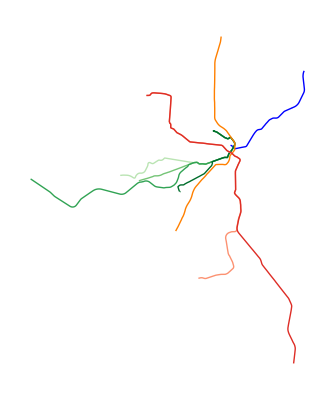

```mathematica
simpleGraphicsObject=Graphics[Normal[GeoGraphics[{Thick,Thread[{orderedCols,Values[orderedLineGraphics]/.Line[x_]:>Line[GeoPosition@*Reverse/@x]}]},GeoBackground->None]][[1,1,1,2,1]]]
```

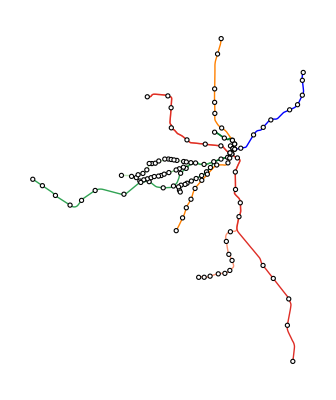

```mathematica
geographicWithStations=Graphics[Normal[GeoGraphics[{Thick,Thread[{orderedCols,Values[orderedLineGraphics]/.Line[x_]:>Line[GeoPosition@*Reverse/@x]}],Map[{EdgeForm[Black],FaceForm[White],Table[Disk[loc,1/500],{loc,cleanedUpStationsByLine[#][[All,3]]}]}&,cleanedUpStationsByLine//Keys]},GeoBackground->None]][[1,1,1,2,1]]]
```

```mathematica
Export["graphics-object.svg",geographicWithStations]
```

graphics-object.svg

```mathematica
Directory[]//SystemOpen
```

```mathematica
nearestLines=Nearest@*First/@orderedLineGraphics;
```

```mathematica
cleanedUpStationsByLineFinelyGrained=Join[cleanedUpStationsByLine,
<|"RED-A"->Select[cleanedUpStationsByLine["RED"],MemberQ[{"Alewife","Davis","Porter","Harvard","Central","Kendall/MIT","Charles/MGH","Park Street","Downtown Crossing","South Station","Broadway","Andrew","JFK/UMass","Savin Hill","Fields Corner","Shawmut","Ashmont","Cedar Grove","Butler","Milton","Central Avenue","Valley Road","Capen Street","Mattapan"},#[[1]]]&],
"RED-B"->Select[cleanedUpStationsByLine["RED"],MemberQ[{"Alewife","Davis","Porter","Harvard","Central","Kendall/MIT","Charles/MGH","Park Street","Downtown Crossing","South Station","Broadway","Andrew","JFK/UMass","North Quincy","Wollaston","Quincy Center","Quincy Adams","Braintree"},#[[1]]]&],

"GREEN-B"->Select[cleanedUpStationsByLine["GREEN"],MemberQ[{"Lechmere","Science Park","North Station","Haymarket","Government Center","Park Street","Boylston","Arlington","Copley","Hynes Convention Center","Kenmore","Blandford Street","Boston University East","Boston University Central","Boston University West","Saint Paul Street","Pleasant Street","Babcock Street","Packards Corner","Harvard Avenue","Griggs Street","Allston Street","Warren Street","Washington Street","Sutherland Road","Chiswick Road","Chestnut Hill Avenue","South Street","Boston College"},#[[1]]]&],
"GREEN-C"->Select[cleanedUpStationsByLine["GREEN"],MemberQ[{"Lechmere","Science Park","North Station","Haymarket","Government Center","Park Street","Boylston","Arlington","Copley","Hynes Convention Center","Kenmore","Saint Marys Street","Hawes Street","Kent Street",(*"Saint Paul Street",*)"Coolidge Corner","Summit Ave/Winchester St","Brandon Hall","Fairbanks Street","Washington Square","Tappan Street","Dean Road","Englewood Avenue","Cleveland Circle"},#[[1]]]&],
"GREEN-D"->Select[cleanedUpStationsByLine["GREEN"],MemberQ[{"Lechmere","Science Park","North Station","Haymarket","Government Center","Park Street","Boylston","Arlington","Copley","Hynes Convention Center","Kenmore","Fenway Park","Longwood","Brookline Village","Brookline Hills","Beaconsfield","Reservoir","Chestnut Hill","Newton Centre","Newton Highlands","Eliot","Waban","Woodland","Riverside"},#[[1]]]&],
"GREEN-E"->Select[cleanedUpStationsByLine["GREEN"],MemberQ[{"Lechmere","Science Park","North Station","Haymarket","Government Center","Park Street","Boylston","Arlington","Copley","Prudential","Symphony","Northeastern","Museum Of Fine Arts","Longwood Medical Area","Brigham Circle","Fenwood Road","Mission Park","Riverway","Back Of The Hill","Heath Street"},#[[1]]]&]
|>];
```

```mathematica
lineAtStation[line_,stationIndex_]:=Block[{station,pos,name,pt},
station=cleanedUpStationsByLineFinelyGrained[line][[stationIndex]];
pt=Reverse[station[[3,1]]];
name=station[[1]];
pos=First[FirstPosition[First[orderedLineGraphics[line]],First@nearestLines[line][pt,1]]];
name->Line[Take[First[orderedLineGraphics[line]],pos]]
]
```

```mathematica
Length/@cleanedUpStationsByLineFinelyGrained
```

<|BLUE→12,GREEN→65,ORANGE→20,RED→29,RED-A→24,RED-B→18,GREEN-B→29,GREEN-C→23,GREEN-D→24,GREEN-E→20|>

```mathematica
stations=<|
"RED-A"->Sort[((ArcLength/@Association[lineAtStation["RED-A",#]&/@Range[24]])/._ArcLength:>0)/ArcLength[orderedLineGraphics["GREEN-E"]]],
"RED-B"->Sort[((ArcLength/@Association[lineAtStation["RED-B",#]&/@Range[18]])/._ArcLength:>0)/ArcLength[orderedLineGraphics["GREEN-E"]]],
"BLUE"->Sort[((ArcLength/@Association[lineAtStation["BLUE",#]&/@Range[12]])/._ArcLength:>0)/ArcLength[orderedLineGraphics["GREEN-E"]]],
"ORANGE"->Sort[((ArcLength/@Association[lineAtStation["ORANGE",#]&/@Range[20]])/._ArcLength:>0)/ArcLength[orderedLineGraphics["GREEN-E"]]],
"GREEN-B"->Sort[((ArcLength/@Association[lineAtStation["GREEN-B",#]&/@Range[29]])/._ArcLength:>0)/ArcLength[orderedLineGraphics["GREEN-E"]]],
"GREEN-C"->Sort[((ArcLength/@Association[lineAtStation["GREEN-C",#]&/@Range[23]])/._ArcLength:>0)/ArcLength[orderedLineGraphics["GREEN-E"]]],
"GREEN-D"->Sort[((ArcLength/@Association[lineAtStation["GREEN-D",#]&/@Range[24]])/._ArcLength:>0)/ArcLength[orderedLineGraphics["GREEN-E"]]],
"GREEN-E"->Sort[((ArcLength/@Association[lineAtStation["GREEN-E",#]&/@Range[20]])/._ArcLength:>0)/ArcLength[orderedLineGraphics["GREEN-E"]]]
|>;
```

```mathematica
trackLength=Normalize[ArcLength/@orderedLineGraphics,Min]
```

<|BLUE→1.06321,GREEN-B→1.54599,GREEN-C→1.30488,GREEN-D→2.57597,GREEN-E→1.,ORANGE→1.83468,RED-A→2.56284,RED-B→3.0585|>

```mathematica
connector[y1_,y2_,{x0_,x1_,length_}]:=
Append[Prepend[Table[{t+x0,y1+(y2-y1) LogisticSigmoid[Rescale[t,{x1-3/8,x1+3/8},{-25,25}]]},{t,Subdivide[x1-3/8,x1+3/8,50]}],{x0,y1}],{x0+length,y2}]
```

```mathematica
stationTract=AssociationThread[#[[All,1]]->Keys[censusTractsRegionMembers][[First/@SortBy[Position[Through[Values[censusTractsRegionMembers][#[[All,3,1]]]],True],Last]]]]&/@KeyDrop[cleanedUpStationsByLineFinelyGrained,{"GREEN","RED"}];
```

```mathematica
medianIncomeSparkLine[line_,{x0_,y0_}]:=DeleteCases[Thread[{x0+stations[line]//Values,y0+Rescale[Lookup[AssociationThread[data[[All,3]]->data[[All,12]]],Lookup[stationTract[line],stations[line]//Keys]]/.""->Missing[],{0,200000},{0,0.5}]}],{a_,Plus[_,Times[_,_Missing]]}]
```

```mathematica
medianIncomeSparkLineGraphicsObjects[line_,{x0_,y0_},col_]:={ListStepPlot[medianIncomeSparkLine[line,{x0,y0}],Center,Filling->y0,Axes->False,PlotStyle->Directive[Thick,col]][[1]],{EdgeForm[Black],FaceForm[White],Disk[#,0.015]&/@medianIncomeSparkLine[line,{x0,y0}]}}
```

```mathematica
cleanerDraft=Graphics[{CapForm["Round"],
{orderedCols[[1]],Thickness[0.0075],Line@connector[0,0,{4.25,0.51,trackLength["BLUE"]}],medianIncomeSparkLineGraphicsObjects["BLUE",{4.25,-0.65},orderedCols[[1]]]},
{orderedCols[[2]],Thickness[0.0075],Line@connector[-1.35,-1.35,{0,0.625,trackLength["GREEN-B"]}],medianIncomeSparkLineGraphicsObjects["GREEN-B",{0,-2},orderedCols[[2]]]},
{orderedCols[[3]],Thickness[0.0075],Line@connector[-1.35,-1.35+0.08,{0,0.625,trackLength["GREEN-C"]}],medianIncomeSparkLineGraphicsObjects["GREEN-C",{0,-2},orderedCols[[3]]]},
{orderedCols[[4]],Thickness[0.0075],Line@connector[-1.35,-1.35+2 0.08,{0,0.625,trackLength["GREEN-D"]}],medianIncomeSparkLineGraphicsObjects["GREEN-D",{0,-2},orderedCols[[4]]]},
{orderedCols[[5]],Thickness[0.0075],Line@connector[-1.35,-1.35+3 0.08,{0,0.52,trackLength["GREEN-E"]}],medianIncomeSparkLineGraphicsObjects["GREEN-E",{0,-2},orderedCols[[5]]]},
{orderedCols[[6]],Thickness[0.0075],Line@connector[-1.35,-1.35,{4.25+trackLength["BLUE"]-trackLength["ORANGE"],0.51,trackLength["ORANGE"]}],medianIncomeSparkLineGraphicsObjects["ORANGE",{4.25+trackLength["BLUE"]-trackLength["ORANGE"],-2},orderedCols[[6]]]},
{orderedCols[[7]],Thickness[0.0075],Line@connector[0,0.08,{0,1.65,trackLength["RED-A"]}],medianIncomeSparkLineGraphicsObjects["RED-A",{0,-0.65},orderedCols[[7]]]},
{orderedCols[[8]],Thickness[0.0075],Line@connector[0,0,{0,1.65,trackLength["RED-B"]}],medianIncomeSparkLineGraphicsObjects["RED-B",{0,-0.65},orderedCols[[8]]]}
,
{EdgeForm[Black],FaceForm[White],
Disk[{#+4.25+trackLength["BLUE"]-trackLength["ORANGE"],-1.35},0.015]&/@Values[stations["ORANGE"]],
Disk[{#+4.25,0},0.015]&/@Values[stations["BLUE"]],
Disk[{#,0},0.015]&/@Values[stations["RED-B"]],
Disk[{#,0.08},0.015]&/@Values[Select[stations["RED-A"],#>1.65&]],
Disk[{#,-1.35},0.015]&/@Values[stations["GREEN-B"]],
Disk[{#,-1.35+0.08},0.015]&/@Values[Select[stations["GREEN-C"],#>0.65&]],
Disk[{#,-1.35+2 0.08},0.015]&/@Values[Select[stations["GREEN-D"],#>0.65&]],
Disk[{#,-1.35+3 0.08},0.015]&/@Values[Select[stations["GREEN-E"],#>0.6&]],
Disk[{#,-1.35+2 0.08},0.015]&/@Values[Select[stations["GREEN-E"],0.6>#>0.5&]]}
},ImageSize->1250]
```

```mathematica
medianIncomeSparkLine[line_,{x0_,y0_}]:=DeleteCases[Thread[{x0+stations[line]//Values,y0+Rescale[Lookup[AssociationThread[data[[All,3]]->data[[All,12]]],Lookup[stationTract[line],stations[line]//Keys]]/.""->Missing[],{0,200000},{0,0.5}]}],{a_,Plus[_,Times[_,_Missing]]}]
```

```mathematica
cleanerDraft=Graphics[{CapForm["Round"],
{orderedCols[[1]],Thickness[0.0075],Line@connector[0,0,{4.25,0.51,trackLength["BLUE"]}],medianIncomeSparkLineGraphicsObjects["BLUE",{4.25,-0.65},orderedCols[[1]]]},
{orderedCols[[2]],Thickness[0.0075],Line@connector[-1.35,-1.35,{0,0.625,trackLength["GREEN-B"]}],medianIncomeSparkLineGraphicsObjects["GREEN-B",{0,-2},orderedCols[[2]]]},
{orderedCols[[3]],Thickness[0.0075],Line@connector[-1.35,-1.35+0.08,{0,0.625,trackLength["GREEN-C"]}],medianIncomeSparkLineGraphicsObjects["GREEN-C",{0,-2},orderedCols[[3]]]},
{orderedCols[[4]],Thickness[0.0075],Line@connector[-1.35,-1.35+2 0.08,{0,0.625,trackLength["GREEN-D"]}],medianIncomeSparkLineGraphicsObjects["GREEN-D",{0,-2},orderedCols[[4]]]},
{orderedCols[[5]],Thickness[0.0075],Line@connector[-1.35,-1.35+3 0.08,{0,0.52,trackLength["GREEN-E"]}],medianIncomeSparkLineGraphicsObjects["GREEN-E",{0,-2},orderedCols[[5]]]},
{orderedCols[[6]],Thickness[0.0075],Line@connector[-1.35,-1.35,{4.25+trackLength["BLUE"]-trackLength["ORANGE"],0.51,trackLength["ORANGE"]}],medianIncomeSparkLineGraphicsObjects["ORANGE",{4.25+trackLength["BLUE"]-trackLength["ORANGE"],-2},orderedCols[[6]]]},
{orderedCols[[7]],Thickness[0.0075],Line@connector[0,0.08,{0,1.65,trackLength["RED-A"]}],medianIncomeSparkLineGraphicsObjects["RED-A",{0,-0.65},orderedCols[[7]]]},
{orderedCols[[8]],Thickness[0.0075],Line@connector[0,0,{0,1.65,trackLength["RED-B"]}],medianIncomeSparkLineGraphicsObjects["RED-B",{0,-0.65},orderedCols[[8]]]}
,
{EdgeForm[Black],FaceForm[White],
Disk[{#+4.25+trackLength["BLUE"]-trackLength["ORANGE"],-1.35},0.015]&/@Values[stations["ORANGE"]],
Disk[{#+4.25,0},0.015]&/@Values[stations["BLUE"]],
Disk[{#,0},0.015]&/@Values[stations["RED-B"]],
Disk[{#,0.08},0.015]&/@Values[Select[stations["RED-A"],#>1.65&]],
Disk[{#,-1.35},0.015]&/@Values[stations["GREEN-B"]],
Disk[{#,-1.35+0.08},0.015]&/@Values[Select[stations["GREEN-C"],#>0.65&]],
Disk[{#,-1.35+2 0.08},0.015]&/@Values[Select[stations["GREEN-D"],#>0.65&]],
Disk[{#,-1.35+3 0.08},0.015]&/@Values[Select[stations["GREEN-E"],#>0.6&]],
Disk[{#,-1.35+2 0.08},0.015]&/@Values[Select[stations["GREEN-E"],0.6>#>0.5&]]}
},ImageSize->1250]
```

```mathematica
Keys/@stationsStandardized
```

## Station Validations

```mathematica
standardizeString[str_]:=ToLowerCase[StringReplace[str,{"/"-> " ","Ave."->"ave"}]/."State"->"State Street"]
```

```mathematica
stationValidationsData = MapAt[standardizeString,Import["data/mbta-gated-station-validations-by-station-01_2018-03_2021.csv","HeaderLines"->1],{All,2}];
stationValidationsDataGroupedByStation=GroupBy[MapAt[DateObject,stationValidationsData,{All,1}],#[[2]]&]//Quiet;
stationValidationsDataGroupedByStation=Map[Delete[#,2]&,stationValidationsDataGroupedByStation,{2}];
```

```mathematica
stationValidationsDataNoWeekends=Map[Select[#,First[#]["DayName"]≠Saturday&&First[#]["DayName"]≠Sunday&]&,stationValidationsDataGroupedByStation];
stationValidationsDataWeekMovingAverage=TimeSeriesResample[TimeSeries[MovingMap[Mean,#,{Quantity[2,"Weeks"],Right}]]]&/@stationValidationsDataNoWeekends;
stationValidationsDataWeekMovingAverage=Interpolation[#["Path"],InterpolationOrder->1,"ExtrapolationHandler"->{Indeterminate&,"WarningMessage"->False}]&/@stationValidationsDataWeekMovingAverage;
```

$Aborted

```mathematica
FromAbsoluteTime/@stationValidationsDataWeekMovingAverage["alewife"][[1,1]]
seasonallyAdjustedDates=Range[#1+365 24 60 60,#2-13 24 60 60,24 60 60]&@@stationValidationsDataWeekMovingAverage["airport"][[1,1]];
```

{Mon 15 Jan 2018 00:00:00GMT-4,Fri 26 Mar 2021 00:00:00GMT-4}

```mathematica
seasonallyAdjustedValidationsTimeseries[station_]:=TimeSeries[Thread[{FromAbsoluteTime/@seasonallyAdjustedDates,100.((stationValidationsDataWeekMovingAverage[station][seasonallyAdjustedDates]-stationValidationsDataWeekMovingAverage[station][seasonallyAdjustedDates-365 24 60 60])/stationValidationsDataWeekMovingAverage[station][seasonallyAdjustedDates-365 24 60 60])}]]
```

```mathematica
smallMultiplesPlot[station_]:=ListLinePlot[seasonallyAdjustedValidationsTimeseries[station],PlotRange->{seasonallyAdjustedDates[[{1,-1}]],{-125,50}},PlotLabel->station,Axes->False,ImageSize->100,PlotStyle->RandomColor[]]
```

```mathematica
Multicolumn[smallMultiplesPlot/@Keys[stationValidationsDataWeekMovingAverage],13,Appearance->"Horizontal"]
```

Seems like we need to drop some stations

Wollaston was undergoing renovations for much of this time-period

Lechmere and Science Park stations closed down for renovations early in the pandemic

There’s some Silver line stations which we don’t concern ourselves with

```mathematica
Extract[stationValidationsDataGroupedByStation//Keys,Position[Length/@Position[Map[standardizeString,Keys/@stations,{2}],#]&/@Keys[stationValidationsDataGroupedByStation],{}]]
```

{courthouse,world trade center}

```mathematica
validationsTimeSeries=KeyDrop[Map[#->seasonallyAdjustedValidationsTimeseries[#]&,stationValidationsDataGroupedByStation//Keys],{"courthouse","world trade center","lechmere","wollaston","science park"}];
validationsTimeSeriesByLine=Lookup[validationsTimeSeries,#]&/@Map[standardizeString,Keys/@stations,{2}];
```

Unfortunately there’s a bunch of missing data..

```mathematica
missingValidationData=(Select[#,MissingQ]&/@validationsTimeSeriesByLine)/.Missing["KeyAbsent",a_]:>a;
stationsStandardized=KeyMap[standardizeString,#]&/@stations;
```

```mathematica
missingTimeSeries=With[{ts=validationsTimeSeries["airport"]},
TimeSeries[Thread[{validationsTimeSeries["airport"]["Times"],0.}]]]
```

TimeSeries[…]

```mathematica
parseTimeSeries[ts_]:=Select[Flatten/@MapAt[Take[First[#],3]&,ts["DatePath"],{All,1}],#[[1]]>2019&]
validationsTimeSeriesByLineTakeTwo=AssociationThread[#,Lookup[validationsTimeSeries,#,missingTimeSeries]]&/@Map[standardizeString,Keys/@stations,{2}];
validationsTimeSeriesByLineTakeTwo=Map[parseTimeSeries,validationsTimeSeriesByLineTakeTwo,{2}];
```

```mathematica
medianIncome[line_]:=AssociationThread[standardizeString/@Keys[stations[line]],Lookup[AssociationThread[data[[All,3]]->data[[All,12]]],Lookup[stationTract[line],stations[line]//Keys]]]
```

```mathematica
tabularValidations=Flatten[Table[
KeyValueMap[Transpose[Join[Transpose[#2],{ConstantArray[standardizeString[station],Length[#2]],ConstantArray[#1,Length[#2]],ConstantArray[stationsStandardized[station][#1],Length[#2]],ConstantArray[medianIncome[station][#1],Length[#2]]}]]&,validationsTimeSeriesByLineTakeTwo[station]],{station,Keys[validationsTimeSeriesByLineTakeTwo]}],2];
```

```mathematica
Export["data/tabular-station-validations-plus-income.csv",Prepend[tabularValidations,{"year","month","day","validation_change","line","station","projected_x","median_income"}]]
```

data/tabular-station-validations-plus-income.csv

```mathematica
Graphics[{CapForm["Round"],
{orderedCols[[1]],Thickness[0.0075],Line@connector[0,0,{4.25,0.51,trackLength["BLUE"]}],medianIncomeSparkLineGraphicsObjects["BLUE",{4.25,-0.65},orderedCols[[1]]]},
{orderedCols[[2]],Thickness[0.0075],Line@connector[-1.35,-1.35,{0,0.625,trackLength["GREEN-B"]}],medianIncomeSparkLineGraphicsObjects["GREEN-B",{0,-2},orderedCols[[2]]]},
{orderedCols[[3]],Thickness[0.0075],Line@connector[-1.35,-1.35+0.08,{0,0.625,trackLength["GREEN-C"]}],medianIncomeSparkLineGraphicsObjects["GREEN-C",{0,-2},orderedCols[[3]]]},
{orderedCols[[4]],Thickness[0.0075],Line@connector[-1.35,-1.35+2 0.08,{0,0.625,trackLength["GREEN-D"]}],medianIncomeSparkLineGraphicsObjects["GREEN-D",{0,-2},orderedCols[[4]]]},
{orderedCols[[5]],Thickness[0.0075],Line@connector[-1.35,-1.35+3 0.08,{0,0.52,trackLength["GREEN-E"]}],medianIncomeSparkLineGraphicsObjects["GREEN-E",{0,-2},orderedCols[[5]]]},
{orderedCols[[6]],Thickness[0.0075],Line@connector[-1.35,-1.35,{4.25+trackLength["BLUE"]-trackLength["ORANGE"],0.51,trackLength["ORANGE"]}],medianIncomeSparkLineGraphicsObjects["ORANGE",{4.25+trackLength["BLUE"]-trackLength["ORANGE"],-2},orderedCols[[6]]]},
{orderedCols[[7]],Thickness[0.0075],Line@connector[0,0.08,{0,1.65,trackLength["RED-A"]}],medianIncomeSparkLineGraphicsObjects["RED-A",{0,-0.65},orderedCols[[7]]]},
{orderedCols[[8]],Thickness[0.0075],Line@connector[0,0,{0,1.65,trackLength["RED-B"]}],medianIncomeSparkLineGraphicsObjects["RED-B",{0,-0.65},orderedCols[[8]]]}
,
{EdgeForm[Black],FaceForm[White],
Disk[{#+4.25+trackLength["BLUE"]-trackLength["ORANGE"],-1.35},0.015]&/@Values[stations["ORANGE"]],
Disk[{#+4.25,0},0.015]&/@Values[stations["BLUE"]],
Disk[{#,0},0.015]&/@Values[stations["RED-B"]],
Disk[{#,0.08},0.015]&/@Values[Select[stations["RED-A"],#>1.65&]],
Disk[{#,-1.35},0.015]&/@Values[stations["GREEN-B"]],
Disk[{#,-1.35+0.08},0.015]&/@Values[Select[stations["GREEN-C"],#>0.65&]],
Disk[{#,-1.35+2 0.08},0.015]&/@Values[Select[stations["GREEN-D"],#>0.65&]],
Disk[{#,-1.35+3 0.08},0.015]&/@Values[Select[stations["GREEN-E"],#>0.6&]],
Disk[{#,-1.35+2 0.08},0.015]&/@Values[Select[stations["GREEN-E"],0.6>#>0.5&]]},

{EdgeForm[Black],FaceForm[Black],
Disk[{#+4.25+trackLength["BLUE"]-trackLength["ORANGE"],-1.35},0.015]&/@Lookup[stationsStandardized["ORANGE"],missingValidationData["ORANGE"],Nothing],
Disk[{#+4.25,0},0.015]&/@Lookup[stationsStandardized["BLUE"],missingValidationData["BLUE"],Nothing],
Disk[{#,0},0.015]&/@Lookup[stationsStandardized["RED-B"],missingValidationData["RED-B"],Nothing],
Disk[{#,0.08},0.015]&/@Lookup[Select[stationsStandardized["RED-A"],#>1.65&],missingValidationData["RED-A"],Nothing],
Disk[{#,-1.35},0.015]&/@Lookup[stationsStandardized["GREEN-B"],missingValidationData["GREEN-B"],Nothing],
Disk[{#,-1.35+0.08},0.015]&/@Lookup[Select[stationsStandardized["GREEN-C"],#>0.65&],missingValidationData["GREEN-C"],Nothing],
Disk[{#,-1.35+2 0.08},0.015]&/@Lookup[Select[stationsStandardized["GREEN-D"],#>0.65&],missingValidationData["GREEN-D"],Nothing],
Disk[{#,-1.35+3 0.08},0.015]&/@Lookup[Select[stationsStandardized["GREEN-E"],#>0.6&],missingValidationData["GREEN-E"],Nothing]}
},ImageSize->1250]
```

### Curating data for redline B

```mathematica
Length[validationsTimeSeries["airport"]//Values]
```

789

```mathematica
(validationsTimeSeries["airport"]//Values)[[425]]
```

2.6201

```mathematica
Values[stations["RED-B"]]
```

{0.,0.215153,0.346706,0.486603,0.667642,0.864672,1.02696,1.13402,1.15496,1.21134,1.34679,1.48033,1.61193,2.19033,2.32879,2.54976,2.76022,3.0585}

```mathematica
Keys[stations["RED-B"]]
```

{Alewife,Davis,Porter,Harvard,Central,Kendall/MIT,Charles/MGH,Park Street,Downtown Crossing,South Station,Broadway,Andrew,JFK/UMass,North Quincy,Wollaston,Quincy Center,Quincy Adams,Braintree}

```mathematica
missingValidationData
```

<|RED-A→{cedar grove,butler,milton,central avenue,valley road,capen street,mattapan},RED-B→{wollaston},BLUE→{},ORANGE→{},GREEN-B→{lechmere,science park,blandford street,boston university east,boston university central,boston university west,babcock street,pleasant street,saint paul street,packards corner,harvard avenue,griggs street,allston street,warren street,washington street,sutherland road,chiswick road,chestnut hill avenue,south street,boston college},GREEN-C→{lechmere,science park,saint marys street,hawes street,kent street,coolidge corner,summit ave winchester st,brandon hall,fairbanks street,washington square,tappan street,dean road,englewood avenue,cleveland circle},GREEN-D→{lechmere,science park,fenway park,longwood,brookline village,brookline hills,beaconsfield,reservoir,chestnut hill,newton centre,newton highlands,eliot,waban,woodland},GREEN-E→{lechmere,science park,northeastern,museum of fine arts,longwood medical area,brigham circle,fenwood road,mission park,riverway,back of the hill,heath street}|>

```mathematica
redBStations = standardizeString@Keys[stations["RED-B"]]
```

{alewife,davis,porter,harvard,central,kendall mit,charles mgh,park street,downtown crossing,south station,broadway,andrew,jfk umass,north quincy,wollaston,quincy center,quincy adams,braintree}

```mathematica
redBLiveIndices = Position[Not@MemberQ[missingValidationData["RED-B"],#]&/@redBStations,True]//Flatten
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,16,17,18}

```mathematica
redBLiveStations = redBStations[[redBLiveIndices]]
```

{alewife,davis,porter,harvard,central,kendall mit,charles mgh,park street,downtown crossing,south station,broadway,andrew,jfk umass,north quincy,quincy center,quincy adams,braintree}

```mathematica
redBLiveLocations = Values[stations["RED-B"]]
```

{0.,0.215153,0.346706,0.486603,0.667642,0.864672,1.02696,1.13402,1.15496,1.21134,1.34679,1.48033,1.61193,2.19033,2.32879,2.54976,2.76022,3.0585}

```mathematica
redBLiveTimeSeries = validationsTimeSeries[[redBLiveStations]];
```

```mathematica
Export["data/redBTimeSeries.json",1+0.01*Values[#]&/@(redBLiveTimeSeries//Values)//Transpose]
```

data/redBTimeSeries.json

### Making Clean JSON for all Station Data

```mathematica
standardizedStations = <|#->AssociationThread[standardizeString@Keys[stations[#]]->Values[stations[#]]]&/@Keys[stations]|>;
```

```mathematica
standardizedStations["RED-A"]=KeyDrop[standardizedStations["RED-A"],Select[Keys[standardizedStations["RED-A"]],MemberQ[standardizedStations["RED-B"]//Keys,#]&][[;;-2]]];
standardizedStations["RED-A"]=KeyDrop[standardizedStations["RED-A"],Select[Keys[standardizedStations["RED-A"]],MemberQ[missingValidationData["RED-A"],#]&]];
standardizedStations["RED-B"] = KeyDrop[standardizedStations["RED-B"],Select[standardizedStations["RED-B"]//Keys,MemberQ[missingValidationData["RED-B"],#]&]];
standardizedStations["GREEN-B"]=KeyDrop[standardizedStations["GREEN-B"],Select[standardizedStations["GREEN-B"]//Keys,MemberQ[Join[standardizedStations["GREEN-C"]//Keys,missingValidationData["GREEN-B"]],#]&]];
standardizedStations["GREEN-C"]=KeyDrop[standardizedStations["GREEN-C"],Select[standardizedStations["GREEN-C"]//Keys,MemberQ[Join[standardizedStations["GREEN-D"]//Keys,missingValidationData["GREEN-C"]],#]&]];
standardizedStations["GREEN-D"]=KeyDrop[standardizedStations["GREEN-D"],Select[standardizedStations["GREEN-D"]//Keys,MemberQ[Join[standardizedStations["GREEN-E"]//Keys,missingValidationData["GREEN-D"]],#]&]];
standardizedStations["GREEN-E"] = KeyDrop[standardizedStations["GREEN-E"],Select[standardizedStations["GREEN-E"]//Keys,MemberQ[missingValidationData["GREEN-E"],#]&]];
standardizedStations["BLUE"] = KeyDrop[standardizedStations["BLUE"],Select[standardizedStations["BLUE"]//Keys,MemberQ[missingValidationData["BLUE"],#]&]];
standardizedStations["ORANGE"] = KeyDrop[standardizedStations["ORANGE"],Select[standardizedStations["ORANGE"]//Keys,MemberQ[missingValidationData["ORANGE"],#]&]];
```

```mathematica
standardizedStations
```

<|RED-A→<|jfk umass→1.60911,savin hill→1.71484,fields corner→1.8756,shawmut→1.98108,ashmont→2.08397|>,RED-B→<|alewife→0.,davis→0.215153,porter→0.346706,harvard→0.486603,central→0.667642,kendall mit→0.864672,charles mgh→1.02696,park street→1.13402,downtown crossing→1.15496,south station→1.21134,broadway→1.34679,andrew→1.48033,jfk umass→1.61193,north quincy→2.19033,quincy center→2.54976,quincy adams→2.76022,braintree→3.0585|>,BLUE→<|bowdoin→0.,government center→0.0330883,state street→0.0537349,aquarium→0.116987,maverick→0.285888,airport→0.403649,wood island→0.50972,orient heights→0.712803,suffolk downs→0.80274,beachmont→0.883249,revere beach→0.998646,wonderland→1.06321|>,ORANGE→<|forest hills→0.,green street→0.118624,stony brook→0.199725,jackson square→0.284017,roxbury crossing→0.376735,ruggles→0.46026,massachusetts ave→0.538309,back bay→0.651774,tufts medical center→0.774691,chinatown→0.815304,downtown crossing→0.856444,state street→0.898659,haymarket→0.941946,north station→0.987523,community college→1.11312,sullivan square→1.26248,assembly→1.34885,wellington→1.44877,malden center→1.70776,oak grove→1.83468|>,GREEN-B→<||>,GREEN-C→<||>,GREEN-D→<|hynes convention center→0.639938,kenmore→0.721984,riverside→2.57597|>,GREEN-E→<|north station→0.213734,haymarket→0.258741,government center→0.297825,park street→0.343713,boylston→0.384345,arlington→0.455672,copley→0.531731,prudential→0.60191,symphony→0.665846|>|>

```mathematica
Export["data/liveStations.json",AssociationMap[(<|"stations"->(standardizedStations[#]//Keys),"locations"->(standardizedStations[#]//Values),"validations"->1+0.01*(Values/@(validationsTimeSeries[[standardizedStations[#]//Keys]]//Values)//Transpose)|>)&,Keys[standardizedStations]]]
```

data/liveStations.json

```mathematica
dataJSON=AssociationMap[(<|"stations"->(standardizedStations[#]//Keys),"locations"->(standardizedStations[#]//Values),"validations"->1+0.01*(Values/@(validationsTimeSeries[[standardizedStations[#]//Keys]]//Values)//Transpose)|>)&,Keys[standardizedStations]]
```

<|RED-A→<|stations→{jfk umass,savin hill,fields corner,shawmut,ashmont},locations→{1},validations→{{1.25364,1.192,1.353,1.1758,1.25733},{1.22489,1.16495,1.30047,1.16374,1.22873},{1.22002,1.1518,1.28185,1.15625,1.22405},783,{0.189809,0.340724,0.384464,0.315718,0.364336},{0.201444,0.349627,0.393628,0.318455,0.373327},{0.214508,0.361008,0.40067,0.325227,0.383046}}|>,6,GREEN-E→<|1|>|>
 |  |  |  |

```mathematica
dataJSON["RED-A"]["validations"]//Dimensions
```

{789,5}